```mathematica
y0=0
```

0

```mathematica
y1=Integrate[x^2+y0^2,x]
```

x^3/3

```mathematica
y2=Integrate[x^2+y1^2,x]
```

x^3/3+x^7/63

```mathematica
y3 = Integrate[x^2+y2^2,x]
```

x^3/3+x^7/63+(2 x^11)/2079+x^15/59535

```mathematica
y4=Integrate[x^2+y3^2,x]
```

x^3/3+x^7/63+(2 x^11)/2079+(13 x^15)/218295+(82 x^19)/37328445+(662 x^23)/10438212015+(4 x^27)/3341878155+x^31/109876902975

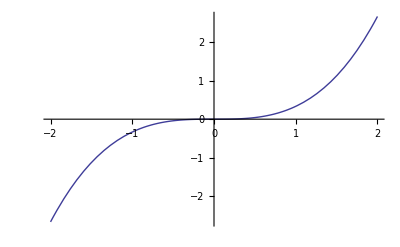

```mathematica
G1=Plot[y1,{x,-2,2},ImageSize->Full]
```

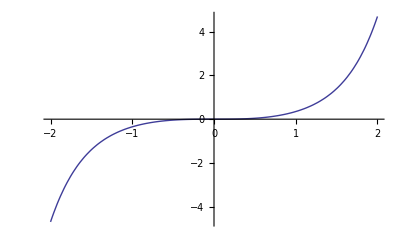

```mathematica
G2=Plot[y2,{x,-2,2},ImageSize->Full]
```

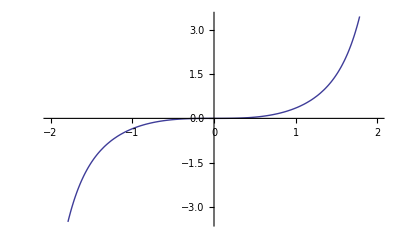

```mathematica
G3=Plot[y3,{x,-2,2},ImageSize->Full]
```

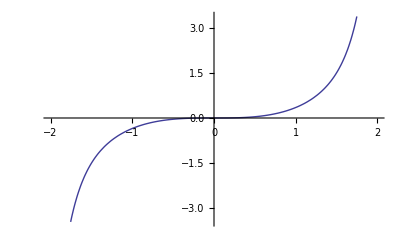

```mathematica
G4=Plot[y4,{x,-2,2},ImageSize->Full]
```

```mathematica
E1 = D[ty[x],x]==ty[x]^2+x^2
```

```mathematica
S1 = DSolve[{E1,ty[0]==10^-19},ty[x],x]
```

```mathematica
y5 = S1[[1,1,2]]
```

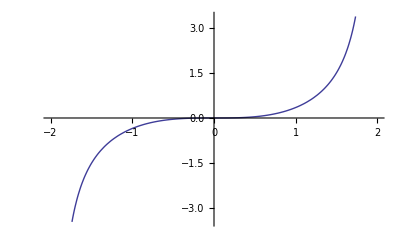

```mathematica
G5=Plot[y5,{x,-2,2},ImageSize->Full]
```

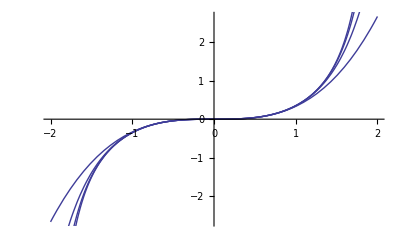

```mathematica
Show[G1,G2,G3,G4,G5]
```